```mathematica
entrop[l_,s_,c_,T_]:=-T*Log[s^l/(l^c)]
```

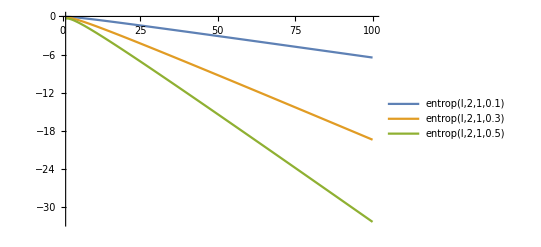

```mathematica
energy[l_,e0_]:=l*e0

Plot[{entrop[l,2,1,0.1],entrop[l,2,1,0.3],entrop[l,2,1,0.5]},{l,1,100},PlotLegends->"Expressions"]
```

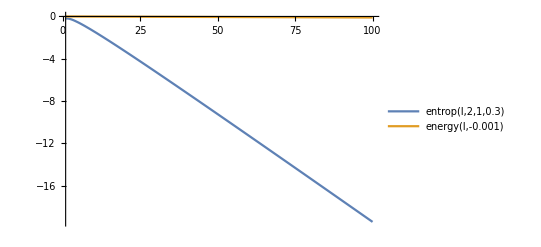

```mathematica
Plot[{entrop[l,2,1,0.3],energy[l,-0.001]},{l,1,100},PlotLegends->"Expressions"]
```

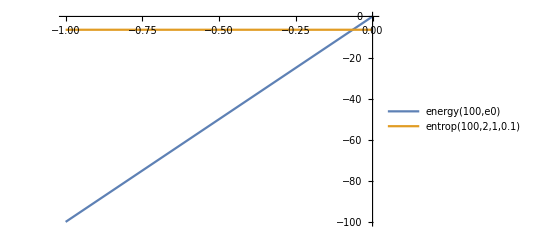

```mathematica
Plot[{energy[100,e0],entrop[100,2,1,0.1]},{e0,0,-1},PlotLegends->"Expressions"]
```